## 1. Обучающий и тестирующий наборы.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P04 GolubovichRoman

```mathematica
Data=Import["NG22P04Problem.xlsx",{"Sheets","ГолубовичРЕ"}];
```

```mathematica
kmSplit[data_]:=Partition[RandomSample[data],UpTo[Round[0.8* Length[data]]]]
```

```mathematica
{Train,Test} = kmSplit[Data];
```

```mathematica
Max[Train[[All,2]]]
```

342.845

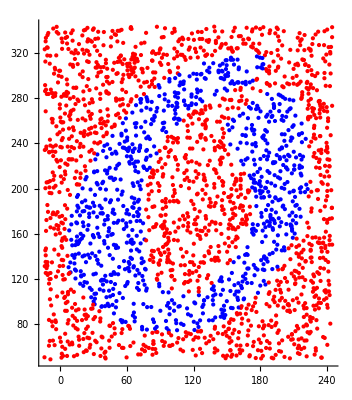

```mathematica
Graphics[MapThread[{#1/.{-1.->Red,1.->Blue},Point[{#2}]}&,{Train[[All,3]],Train[[All,;;2]]}],Axes->True]
```

## 2. Метод k - средних.

```mathematica
friendindex = Flatten[Position[Train[[All,3]],1.]];
```

```mathematica
foeindex = Flatten[Position[Train[[All,3]],-1.]];
```

```mathematica
frienddata = Train[[friendindex,;;2]];
```

```mathematica
foedata = Train[[foeindex,;;2]];
```

```mathematica
friendcenters = RandomSample[frienddata,20];
```

```mathematica
friendtocluster = Flatten[Nearest[friendcenters->"Index",#,1]&/@frienddata];
```

```mathematica
friendclusterindexes = Flatten[Position[friendtocluster,#]]&/@Range[20];
```

```mathematica
newfriendcenters = Mean[frienddata[[#]]]&/@friendclusterindexes
```

{{103.768,267.658},{100.659,97.0185},{41.2393,121.455},{166.533,121.244},{30.5562,99.0989},{19.7647,162.508},{115.968,292.029},{185.568,191.322},{209.152,211.787},{148.262,306.794},{50.8759,157.619},{128.265,91.3553},{54.2578,101.235},{73.0348,261.627},{174.128,288.591},{79.8433,88.0687},{54.75,208.686},{13.7554,138.508},{179.033,251.653},{30.5779,105.274}}

```mathematica
friendcenters = RandomSample[frienddata,20]; friendcenters2 ={};
While[friendcenters=!=friendcenters2,
friendtocluster = Flatten[Nearest[friendcenters->"Index",#,1]&/@frienddata];
friendclusterindexes = Flatten[Position[friendtocluster,#]]&/@Range[20];
friendcenters2 = friendcenters;
friendcenters = Mean[frienddata[[#]]]&/@friendclusterindexes;
]
```

```mathematica
foecenters= RandomSample[foedata,40]; foecenters2 ={};
While[foecenters=!=foecenters2,
foetocluster = Flatten[Nearest[foecenters->"Index",#,1]&/@foedata];
foeclusterindexes = Flatten[Position[foetocluster,#]]&/@Range[40];
foecenters2 = foecenters;
foecenters = Mean[foedata[[#]]]&/@foeclusterindexes;
]
```

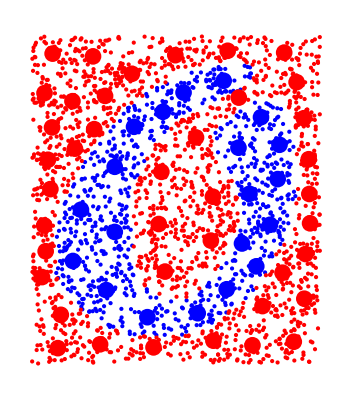

```mathematica
Graphics[{Blue,Point@frienddata,Red,Point@foedata,PointSize[0.03],Blue,Point[friendcenters],Red, Point[foecenters]}]
```

## 3. Зоны влияния.

```mathematica
friendC= Covariance[frienddata[[#]]]&/@friendclusterindexes;
```

```mathematica
foeC= Covariance[foedata[[#]]]&/@foeclusterindexes;
```

```mathematica
friendellipses = Graphics[{Opacity[0.18],Blue,MapThread[Ellipsoid[#1,#2]&,{friendcenters,friendC}],
Opacity[0.12],MapThread[Ellipsoid[#1,4*#2]&,{friendcenters,friendC}],
Opacity[0.06],MapThread[Ellipsoid[#1,9#2]&,{friendcenters,friendC}]}];
```

```mathematica
foeellipses = Graphics[{Opacity[0.18],Red,MapThread[Ellipsoid[#1,#2]&,{foecenters,foeC}],
Opacity[0.12],MapThread[Ellipsoid[#1,4*#2]&,{foecenters,foeC}],
Opacity[0.06],MapThread[Ellipsoid[#1,9#2]&,{foecenters,foeC}]}];
```

```mathematica
allpoints = Graphics[{Blue,Point@frienddata,Red,Point@foedata,PointSize[0.024],Blue,Point[friendcenters],Red, Point[foecenters]}];
```

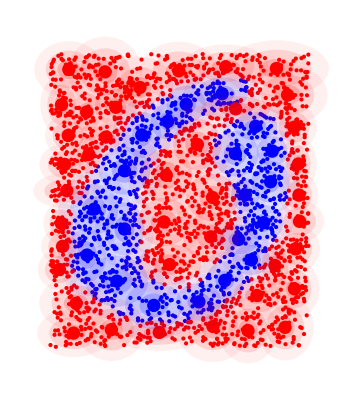

```mathematica
Show[allpoints,friendellipses,foeellipses]
```

## 4. Радиально-базисные функции.

```mathematica
Exp[-1/2*(({x1,x2}-friendcenters[[1]]).Inverse[friendC[[1]]].({x1,x2}-friendcenters[[1]]))]
```

ⅇ^(1/2 (-(-160.926+x1) (0.011227 (-160.926+x1)-0.000125237 (-115.87+x2))-(-0.000125237 (-160.926+x1)+0.0109273 (-115.87+x2)) (-115.87+x2)))

```mathematica
RBF[x_List,s_,m_]:=N@Exp[Expand[-1/2*(Inverse[s^2*(Join[friendC,foeC][[m]])].(x-Join[friendcenters,foecenters][[m]]).(x-Join[friendcenters,foecenters][[m]]))]]
```

```mathematica
Manipulate[Plot3D[RBF[{x,y},s,m],{x,-20,250},{y,20,344},ColorFunction->"GreenPinkTones",PlotRange->All],{{m,1},Range[60],ControlType->Setter},{{s,3},Range[3]}]
```

## 5. Псевдообратная матрица.

```mathematica
tmpmatrix=Table[RBF[#,3,m],{m,1,60}]&/@Train[[All,;;2]];
```

```mathematica
{u,s,v} = SingularValueDecomposition[tmpmatrix];
```

```mathematica
u//Dimensions
```

{2400,2400}

```mathematica
eta = Transpose[u].Train[[All,3]];
```

```mathematica
eta//Dimensions
```

{2400}

```mathematica
eta//Dimensions
```

{2400}

```mathematica
s//Dimensions
```

{2400,60}

```mathematica
signnumbers = s[[#,#]]&/@Range[60]
```

{28.5046,24.0597,22.0186,19.4837,19.1665,16.1079,15.8672,14.4045,13.7779,12.1117,11.9798,11.0174,10.03,9.4312,9.09751,8.1346,7.91666,7.72902,6.86569,6.64709,6.18672,5.99577,5.36957,5.17671,4.93003,4.7,4.47668,4.08703,4.06286,3.78525,3.58855,3.5221,3.36971,3.25069,3.09546,2.84806,2.65167,2.59208,2.35768,2.194,2.16093,2.02792,1.90606,1.84691,1.76582,1.68955,1.52147,1.4785,1.36576,1.28845,1.19811,1.14469,1.12479,0.979875,0.951632,0.847644,0.735343,0.620731,0.601189,0.537782}

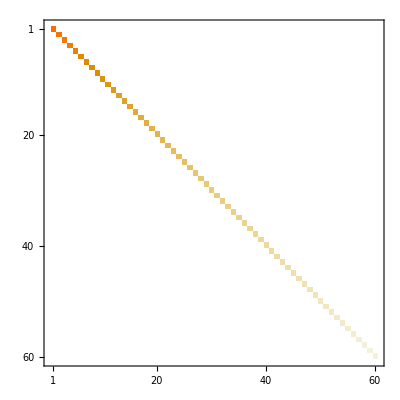

```mathematica
MatrixPlot[s[[;;60,;;60]]]
```

```mathematica
xi =eta[[;;60]]/signnumbers;
```

```mathematica
alpha = v.xi
```

{0.763283,0.728267,-0.0017636,0.901453,0.936501,0.539251,1.76849,0.415278,-2.40583,4.1547,1.73668,1.51563,4.03008,-0.405104,2.07045,3.7133,1.98282,1.27801,-0.955783,1.52694,-0.718204,0.902115,-3.58262,1.74811,-2.44748,-1.24083,-2.42867,-0.0602846,-0.613979,1.35155,-1.51279,-0.788839,-2.20693,-0.280615,-2.01253,-1.24308,2.83581,-0.518873,-3.15439,-0.64056,0.102583,0.674977,-1.19697,-0.528251,-1.217,-5.40458,0.90611,-1.52928,-0.498447,-0.990603,0.787265,-3.25638,3.2114,-4.10967,-1.04358,-1.56764,-0.286795,-1.62619,-0.933461,-1.38798}

```mathematica
Classifier[x_List,s_:3]:=alpha.Table[RBF[x,s,m],{m,1,60}];
```

```mathematica
Classifier[{10,10}]
```

0.018509

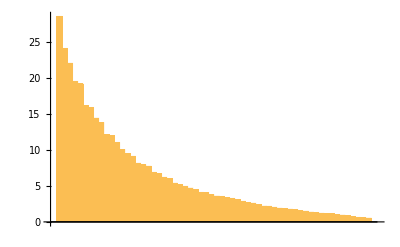

```mathematica
BarChart[Diagonal[s]]
```

## 6. Сеть радиально-базисных функций.

```mathematica
Plot3D[Classifier[{x,y}], {x,-50,300},{y,20,350},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Plot3D[Sign@Classifier[{x,y}], {x,-50,300},{y,20,350},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

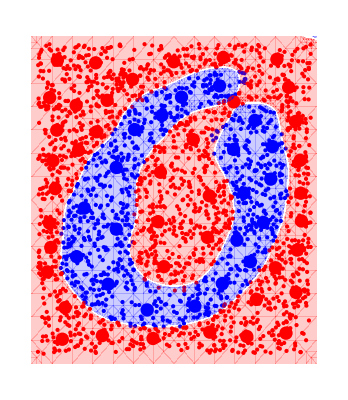

```mathematica
Show[allpoints,ContourPlot[Sign@Classifier[{x,y}], {x,-20,250},{y,40,350},Contours->{0},ContourShading->{{Opacity[0.2],Red},{Opacity[0.2],Blue}}]]
```

## 7. Ошибки первого и второго рода.

```mathematica
friendindextest = Flatten[Position[Test[[All,3]],1.]];
```

```mathematica
foeindextest = Flatten[Position[Test[[All,3]],-1.]];
```

```mathematica
frienddatatest = Test[[friendindextest,;;2]];
```

```mathematica
foedatatest = Test[[foeindextest,;;2]];
```

```mathematica
geterror1[s_]:=Count[Sign[Classifier[#,s]]&/@frienddatatest,-1]/Length[frienddatatest]*100//N
```

```mathematica
geterror2[s_]:=Count[Sign[Classifier[#,s]]&/@foedatatest,1]/Length[foedatatest]*100//N
```

```mathematica
{geterror1[3],geterror2[3]}
```

{2.41546,3.81679}

## 8. Зависимость качества классификатора от размера зоны влияния RBF.

```mathematica
errors = {geterror1[#],geterror2[#]}&/@Range[6];
```

General::munfl: Exp[-950.474] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-803.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-975.254] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
karti = Show[allpoints,ContourPlot[Sign@Classifier[{x,y},#], {x,-20,250},{y,40,350},Contours->{0},ContourShading->{{Opacity[0.2],Red},{Opacity[0.2],Blue}}]]&/@Range[6];
```

General::munfl: Exp[-988.819] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1526.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-831.941] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
vozbud = Plot3D[Classifier[{x,y},#], {x,-50,300},{y,20,350},ColorFunction->"TemperatureMap"]&/@Range[6];
```

General::munfl: Exp[-859.555] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-779.562] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1288.18] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

При S = 3, получеам наименьшие ошибки, при увеличении или уменьшении s ошибки возрастают

```mathematica
allplots = Table[{errors[[i]],vozbud[[i]],karti[[i]]},{i,1,6}]//TableForm;
```

```mathematica
allplots;
```